```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

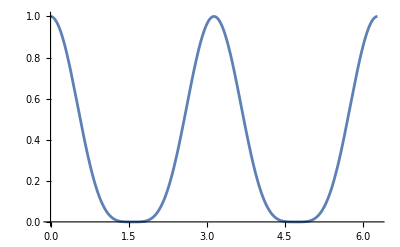

-Graphics-

```mathematica
Plot[Cos[x]^4, {x, 0, 2 Pi}]
Plot[Cos[x]^4, {x, 0, 2 Pi}]
```

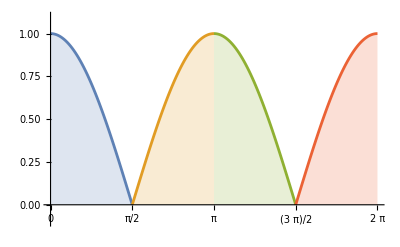

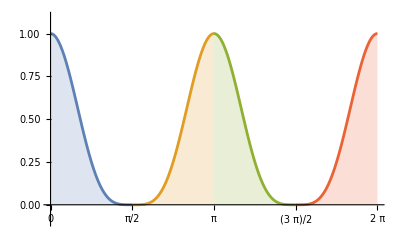

```mathematica
f1= Show[
With[{n=1},
Plot[Abs[Cos[x]],{x,(n-1) Pi/2,n Pi/2},PlotStyle->ColorData[97][n], PlotRange -> {{ 0, 2 Pi }, {-0.1, 1.1}},
Filling -> Axis,
Ticks->{
{0,Pi/2, Pi, 3 Pi/2, 2 Pi}
,Automatic },AxesLabel->{MaTeX["x"],MaTeX["|\\cos(x)|"]}
]
],
Table[
Plot[Abs[Cos[x]],{x,(n-1) Pi/2,n Pi/2},
Filling -> Axis,PlotStyle->ColorData[97][n]]
,{n,2,4}]
]


f2= Show[
With[{n=1},
Plot[Cos[x]^4,{x,(n-1) Pi/2,n Pi/2},PlotStyle->ColorData[97][n], PlotRange -> {{ 0, 2 Pi }, {-0.1, 1.1}},
Filling -> Axis,
Ticks->{
{0,Pi/2, Pi, 3 Pi/2, 2 Pi}
,Automatic },AxesLabel->{MaTeX["x"],MaTeX["\\cos^4(x)"]}
]
],
Table[
Plot[Cos[x]^4,{x,(n-1) Pi/2,n Pi/2},
Filling -> Axis,PlotStyle->ColorData[97][n]]
,{n,2,4}]
]
```

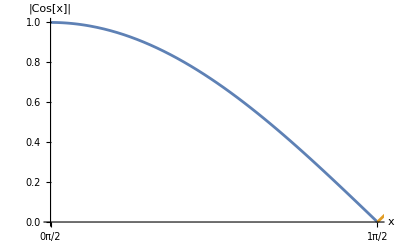

```mathematica
MaTeX[#]&/@ {"0", "\\frac{\\pi}{2}", "\\pi", "\\frac{3\\pi}{2}", "2\\pi"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
peeters`exportForLatex["trigPropFig1",f1]
peeters`exportForLatex["trigPropFig2",f2]
```

{trigPropFig1.eps,trigPropFig1pn.png}

{trigPropFig2.eps,trigPropFig2pn.png}

Of course, could have just done this directly:

```mathematica
s = Integrate[Sin[x]^4, {x, 0,  2 Pi}]
c = Integrate[Cos[x]^4, {x, 0, Pi/2}]
Solve[s == k c, k]
```